# Homework 3

## Exercise 1

### Non-mathematica

P_A = f(c_A, P_B)
P_B = g(c_B, P_A)

dP_A = f_C_AⅆC_A+ f_P_BⅆP_B
dP_B = g_C_BⅆC_B+ g_P_AⅆP_A
where h_x = (∂h)/(∂x)

We can rewrite these as:
ⅆ P_A - f_P_B ⅆ P_B  = f_C_A ⅆ C_A
ⅆ P_B - g_P_A ⅆ P_A = g_C_B ⅆ C_B

Or in matrix form:
(1 | -f_P_B
-g_P_A | 1) (ⅆ P_A
ⅆ P_B) = (f_C_A ⅆ C_A
g_C_B ⅆ C_B)

If we invert the matrix of coefficients we obtain

1/Δ (1 | f_P_B
g_P_A | 1), where Δ = 1 - (f_P_B) (g_P_A)

Multiplying by the inverse, we obtain
(ⅆ P_A
ⅆ P_B) = 1/Δ (1 | f_P_B
g_P_A | 1) (f_C_A ⅆ C_A
g_C_B ⅆ C_B)

(ⅆ P_A
ⅆ P_B) = 1/Δ (f_C_A ⅆ C_A + f_P_B g_C_B ⅆ C_B
g_P_A f_C_A ⅆ C_A + g_C_B ⅆ C_B)

The comparative statics are as follows (assuming, (ⅆ C_B)/(ⅆ C_A) = 0, (ⅆ C_A)/(ⅆ C_B) = 0):

(ⅆ P_A)/(ⅆ C_A) = f_C_A + f_P_B (g_C_B(ⅆ C_B)/(ⅆ C_A)+ g_P_A (ⅆ P_A)/(ⅆ C_A))
(ⅆ P_A)/(ⅆ C_A) = f_C_A + f_P_B g_P_A (ⅆ P_A)/(ⅆ C_A)
(ⅆ P_A)/(ⅆ C_A) -  f_P_B g_P_A (ⅆ P_A)/(ⅆ C_A) = f_C_A
((ⅆ P_A)/(ⅆ C_A)) (1 -  f_P_B g_P_A) =  f_C_A
(ⅆ P_A)/(ⅆ C_A)=  f_C_A/(1-f_P_B g_P_A)
Similarly
(ⅆ P_B)/(ⅆ C_B)=  f_C_B/(1-g_P_B f_P_A)

(ⅆ P_A)/(ⅆ C_B) = f_C_A (ⅆ C_A)/(ⅆ C_B) + f_P_B(g_C_B + g_P_A (ⅆ P_A)/(ⅆ C_B))
(ⅆ P_A)/(ⅆ C_B) = f_P_B(g_C_B + g_P_A (ⅆ P_A)/(ⅆ C_B))
(ⅆ P_A)/(ⅆ C_B) - g_P_A (ⅆ P_A)/(ⅆ C_B)= f_P_Bg_C_B
((ⅆ P_A)/(ⅆ C_B)) (1 - g_P_A) = f_P_Bg_C_B
(ⅆ P_A)/(ⅆ C_B) = (f_P_B g_C_B)/(1-g_P_A)
Similarly
(ⅆ P_B)/(ⅆ C_A) = (g_P_A f_C_A)/(1-f_P_B)

Assuming
f_C_A ≥ 0 (Firm A increases [weakly] prices due to higher production costs)
f_P_B ≥ 0 (Firm A increases [weakly] prices due to higher prices from firm B)
g_C_B ≥ 0 (Firm B increases [weakly] increases prices due to higher production costs)
g_P_A ≥ 0 (Firm B increases [weakly] prices due to higher prices from firm A)

We obtain the following signs
(ⅆ P_A)/(ⅆ C_A) ≥ 0
(ⅆ P_B)/(ⅆ C_B) ≥ 0
(ⅆ P_A)/(ⅆ C_B) ≥ 0
(ⅆ P_B)/(ⅆ C_A) ≥ 0

### Mathematica

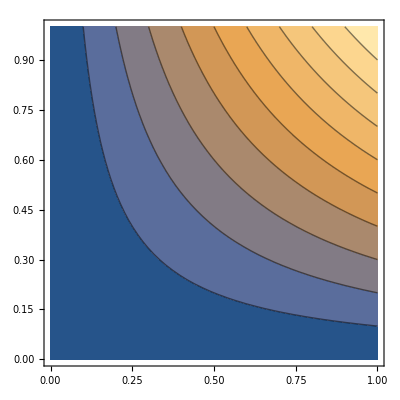

```mathematica
ContourPlot[fpb gcb/(1-0.5), {fpb, 0, 1}, {gcb, 0, 1}] (*set gpa = 0.5 for graphing ease *)
```

## Exercise 2

Maximize x^0.5 y^0.5 such that 2 x + y = k

ℒ (x, y, λ) = x^0.5 y^0.5 + λ (2 x + y - k)

(∂ℒ)/(∂x) = (√y)/(2√x) + 2 λ = 0
(∂ℒ)/(∂y) = ((√x)/(2√y)) + λ = 0
(∂ℒ)/(∂λ) = 2 x + y - k = 0

λ = (-√x)/(2√y)
2 λ =  (-√x)/(√y)
(∂ℒ)/(∂x) = ((√y)/(2 √x)) - (√x)/(√y) = 0
((√y)/(2 √x)) = (√x)/(√y)
y = 2 x
-2 x + y = 0

2 x + y - k = 0
2x + y = k

(-2 | 1
2 | 1) (x
y) = (0
k)

(x
y) = (-1/4 | 1/4
1/2 | 1/2) (0
k) = (-1/4 0+1/4 k
1/2 0 + 1/2 k)
(x
y)  = (k/4
k/2)

## Exercise 3

C(n + 1, k + 1) = ((n + 1)!)/((k + 1)! (n - k)!)
C(n, k) = (n!)/(k!(n-k)!) = (n!)/(k! (n - k) (n-k -1)!) = (n!)/(k! (n - k - 1)!) 1/(n - k)
C(n, k + 1) = (n!)/((k + 1)! (n - k -1)!) = (n!)/((k + 1) k! (n - k - 1)!) = (n!)/(k! (n - k -1)!) 1/(k + 1)
C(n, k) + C(n, k + 1) = (n!)/(k! (n - k -1)!) 1/(k + 1) + (n!)/(k! (n - k - 1)!) 1/(n - k) = (n!)/(k! (n - k -1)!) (1/(k + 1) + 1/(n - k))
= (n!)/(k! (n - k -1)!) ((n - k + k + 1)/((k + 1)(n-k))) = (n!)/(k! (n - k -1)!) ((n + 1)/((k + 1)(n-k))) = ((n + 1)!)/((k + 1)! (n - k)!) = C(n + 1, k + 1)

## Exercise 4

An algebra of sets (σ algebra) of a set X is a collection Σ of subsets of X that is closed under complementation,  union of countably many sets and intersection of countably many sets.
Ω = {1, 2, 3, 4, 5, 6}
E1 = {2, 4, 6}
E2 = {1, 3, 5} 
Σ = {∅, E1, E2, Ω} is an algebra of sets over Ω because:
∅^C = Ω (member of Σ)
Ω^C = ∅ (member of Σ)
E1^C = E2 (member of Σ)
E2^C = E1 (member of Σ)
The intersection of ∅ with any of the other elements in the collection is ∅
The intersection of Ω with any of the other elements in the collection is that element
The union of ∅ with any other of the other elements in the collection is that element
The union of Ω with any other element in the collection is Ω
E1 ∪ E2 = Ω  (member of Σ)
E1 ∩ E2 = ∅  (member of Σ)

Thus the set is closed under the required operations.

Ω = {1, 2, 3, 4, 5, 6}
E1 = {2, 4}
E2 = {1, 3}
Τ =  {∅, E1, E2, Ω} is not an algebra of sets over Ω because E1^C = {1, 3, 5, 6} is not a member of Τ.

## Exercise 5

If 𝒜 is a σ algebra:
1. If 𝒜 is an algebra of sets over Ω then Ω, ∅ ∈ 𝒜
Proof:
	Ω^C = ∅ and vice versa. Ω must be in 𝒜 by finite unions of elements of 𝒜 for 𝒜 to be cosed under finite unions (by definition of closure).
	Another way to prove this is E1 and E1^C must be in 𝒜 (by definiion). E1 ∩ E1^C is ∅. Thus ∅ and ∅^C = Ω must also be in 𝒜.
2. If E1 ∈ 𝒜 and E2 ∈ 𝒜 then E1 ∩ E2 ∈ 𝒜
Proof
If E1 ∩ E2 were not in 𝒜 then it would not be a σ algebra by definition.
Another proof is that E1^C and E2^C must be in 𝒜. E1 ∩ E2 = (E1^C ∪ (E2^C))^C.  (E1^C ∪ (E2^C))^C must also be in 𝒜.
3. If E1 ∈ 𝒜 and E2 ∈ 𝒜 then E1 \ E2 ∈ 𝒜
Proof
E1 \ E2 = E1 ∩ E2^C.
Thus can be rewritten as (E1^C ∪ (E2))^C. E1^C is in 𝒜. Therefore (E1^C ∪ E2) and its complement (E1^C ∪ (E2))^C must be as well.
4. If E_n ∈ 𝒜, then ∪_n^N E_n ∈ 𝒜
Proof by induction:
Base case: If E_1 ∈ 𝒜 ∧ E_2 ∈ 𝒜 ⟶ E_1 ∪ E_2 ∈ 𝒜 (by definition)
Inductive case:  If ∪_(n∈N) E_(n-1) ∈ 𝒜 ∧ E_n ∈ 𝒜 ⟶ ∪_(n∈N) E_(n-1) ∪ E_n ∈ 𝒜 (by definition)
Therefore: ∪_(n ∈ N) E_n

 If E_n ∈ 𝒜, then ∩_n^N E_n ∈ 𝒜
Proof by induction:
Base case: If E_1 ∈ 𝒜 ∧ E_2 ∈ 𝒜 ⟶ E_1 ∩ E_2 ∈ 𝒜 (previously proved)
Inductive case:  If ∪_(n∈N) E_(n-1) ∈ 𝒜 ∧ E_n ∈ 𝒜 ⟶ ∪_(n∈N) E_(n-1) ∩ E_n ∈ 𝒜 (by previous proof)
Therefore: ∩_n^N E_n

## Exercise 6

1. The probability of any event occuring is at least 0.
2. The probability that one of the events occuring (from the list of all possible events) occuring is 1.
3. If events don’t overlap (example of overlapping event: roll an even number or 2), then the probability of the events occuring is the sum of their individual probabilities.

Properties
1. P(E1 ∪ E2) = P(E1) + P(E2)
Proof
P(∪_n^∞ E_N) = ∑_(n=1)^∞ P(E_n)  (axiom 3)
Let E_i = ∅ ∀ i ∈ ℕ, i > 2
P(∪_n^∞ E_N) = P(E1 ∪ E2 ∪_3^∞ E_n) = P(E_1) + P(E_2) + P(E_3) + P(E_4) + ...
P(∅) = P(∅) + P(∅) + ... iff P(∅) = 0 (otherwise the sum diverges)
∴ P(E1 ∪ E2) = P(E_1) + P(E_2) 

2. P(∪_n^N E_n) = ∑_(i=1)^N P(E_n)
by property 1 P(E_(n-1) U E_n) = P(E_(n-1)) + P(E_n)
by propertyb 4 of a σ algebra ∪_n^N E_n ∈ Σ
∴ P(∪_n^N E_n) = ∑_(i=1)^N P(E_n)

3. P(E^C) = 1 - P(E)
P(E^C ∪ E) = P(Ω) = 1 = P(E^C) + P(E)
∴ P(E^C) = 1 - P(E)

4. E1 ⊆ E2, P(E1) ≤ P(E2)
E1  = E2 ∪ (E1 ∪ E2^C)
P(E1) = P(E2) + P(E1 ∪ E2^C) ≥ P(E2)

5. P(A ∪ B) = P(A) + P(B) - P(A ∩ B) 
Proof
P(A ∪ B) =
P((A \ B) ∪ (B \ A) ∪ (A ∩ B)) = 
P((A ∩ B^C) ∪ (B ∪ A^C) ∪ (A ∩ B)) =
P(A ∩ B^C) + (B ∪ A^C) + P (A ∩ B)
P(A) + P(B) - P (A∩B)

## Computational Exercise 1

```mathematica
ClearAll[lst, x, l, square, newList]
lst = Range[0, 15]
newList = {};
Do[AppendTo[newList, x^2], {x, lst}];
StringForm["The squared list using loops: ``", newList]
square [l_]:= (
y = {};
Do[AppendTo[y, x^2],{x, l}];
Return[y]
)
StringForm["The squared list using a function: ``", square[lst]]
StringForm["The squared list using map: ``", Map[#^2&, lst]]
isEven[x_] := If[EvenQ[x], 1, 0]
StringForm["isEven[9] = ``", isEven[9]]
StringForm["isEven[10] = ``", isEven[10]]
StringForm["Picking out the even itmes from the list ``", Pick[lst, Map[isEven, lst], 1]]
```

{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15}

The squared list using loops: {0, 1, 4, 9, 16, 25, 36, 49, 64, 81, 100, 121, 144, 169, 196, 225}

The squared list using a function: {0, 1, 4, 9, 16, 25, 36, 49, 64, 81, 100, 121, 144, 169, 196, 225}

The squared list using map: {0, 1, 4, 9, 16, 25, 36, 49, 64, 81, 100, 121, 144, 169, 196, 225}

isEven[9] = 0

isEven[10] = 1

Picking out the even itmes from the list {0, 2, 4, 6, 8, 10, 12, 14}

## Computational Exercise 2

```mathematica
ClearAll[powerSet, x, y, subsets]
powerSet[s_List] := (
subsets = {{}};
Do[(
newSubsets = {};
Do[(
newSubset = Union[oldSubset, {element}]; 
AppendTo[newSubsets, newSubset];
),{oldSubset, subsets}
];
subsets = Join[subsets, newSubsets];
), {element, s}];
Return[subsets]
)
powerSet[{e1, e2, e3}]
```

{{},{e1},{e2},{e1,e2},{e3},{e1,e3},{e2,e3},{e1,e2,e3}}

## Computational Exercise 3

```mathematica
ClearAll[fiveFlips]
fiveFlips := RandomChoice[{45, 100-45}->{0, 1}, 5];
results = {};
Do[AppendTo[results, fiveFlips], 1000];
headCounts = Sort[Map[Total, results]];
counts = 1/1000. * BinCounts[headCounts, {0, 6, 1}]
StringForm["The empirical PMF is as follows \nP(0) = `1`, P(1) = `2`, P(2) = `3`, P(3) = `4`, P(4) = `5`, P(5) = `6`", counts[[1]], counts[[2]], counts[[3]], counts[[4]], counts[[5]], counts[[6]]]
```

{0.015,0.121,0.283,0.333,0.199,0.049}

The empirical PMF is as follows 
P(0) = 0.015, P(1) = 0.121, P(2) = 0.283, P(3) = 0.333, P(4) = 0.199, P(5) = 0.049

## Computational Exercise 4

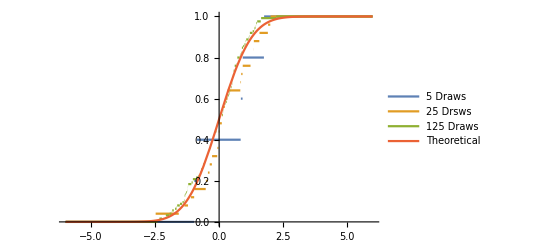

```mathematica
fiveDraws = RandomVariate[NormalDistribution[],5]; (* Take five draws *)
twentyFiveDraws = RandomVariate[NormalDistribution[],25]; (* Take twenty five draws *)
oneTwentyFiveDraws = RandomVariate[NormalDistribution[],125]; (* Take one hunder and twenty five draws *)
d5 = EmpiricalDistribution[fiveDraws]; (* Convert to a random distribution *)
d25 = EmpiricalDistribution[twentyFiveDraws]; (* Convert to a random distribution *)
d125 = EmpiricalDistribution[oneTwentyFiveDraws]; (* Convert to a random distribution *)
(* Plot *)
Plot[{CDF[d5, x],CDF[d25, x], CDF[d125, x], CDF[NormalDistribution[],x]}, {x, -6, 6}, PlotLegends->{"5 Draws", "25 Drsws", "125 Draws", "Theoretical"}, PlotStyle->Thick]
```